# Mathematica: A Problem-Centered Approach Roozbeh Hazrat

## 1 Introduction

1.1 Mathematica as a calculator

```mathematica
10^9-987654321
```

```mathematica
2682440^4+15365639^4+18796760^4
```

```mathematica
20615673^4
```

```mathematica
180630077292169281088848499041
```

```mathematica
2^9941-1
```

```mathematica
PrimeQ[2^9941-1]
```

```mathematica
24/17
```

```mathematica
Sin[Pi/5]
```

```mathematica
N[24/17]
```

```mathematica
N[24/17,20]
```

```mathematica
?N
```

```mathematica
??N
```

```mathematica
Sqrt[(Pi/4)^2+(0.5Log[2])^2]
```

0.858466

### Problem 1.1

```mathematica
Tan[(3Pi)/11]+4sin[(2Pi)/11]
```

```mathematica
Cot[(5 π)/22]+4 sin[(2 π)/11]
?Simplify
```

Cot[(5 π)/22]+4 sin[(2 π)/11]

```mathematica
Simplify[Tan[(3Pi)/11]+4sin[(2Pi)/11]]
```

```mathematica
?FullSimplify
```

```mathematica
FullSimplify[Tan[(3Pi)/11]+4sin[(2Pi)/11]]
```

Cot[(5 π)/22]+4 sin[(2 π)/11]

### Exercise 1.1

```mathematica
Sqrt[(64)^(1/3)(2^2+(1/2)^2)-1]
```

4

### Problem 1.2

```mathematica
4+6/4 *3^-2+1
```

31/6

### TIPS

#### -Graphics-

1.2 Numbers

```mathematica
4!
```

```mathematica
123!
```

```mathematica
(*The fundamental theorem of arithmetic states that one can decompose any
number n as a product of powers of primes and this decomposition is unique*)
FactorInteger[12]
```

```mathematica
FactorInteger[37534]
```

```mathematica
FactorInteger[6473434456376432]
```

```mathematica
Prime[8]
```

```mathematica
PrimeQ[2^(2^1)+1]
```

```mathematica
PrimeQ[2^(2^2)+1]
```

```mathematica
PrimeQ[2^(2^3)+1]
```

```mathematica
PrimeQ[2^(2^4)+1]
```

```mathematica
PrimeQ[2^(2^5)+1]
```

```mathematica
2^(2^5)+1
```

```mathematica
FactorInteger[%]
```

{{641,1},{6700417,1}}

## Problem 1.3

### -Graphics-

```mathematica
10^13-10^12
```

```mathematica
PrimePi[10^13]
```

```mathematica
PrimePi[10^12]
```

```mathematica
N[(346065536839-37607912018)/9000000000000]*100
```

### Exercise 1.2

```mathematica
PrimeQ[123456789098765432111]
```

```mathematica
True
```

### Exercise 1.3

#### -Graphics-

```mathematica
LCM[1,2,3,4,5,6,7,8,9,10]
2^(10-1)
```

### Exercise 1.4

```mathematica
32!
```

## Problem 1.4

### -Graphics-

```mathematica
Mod[98^98*75^75,10^98]
Mod[98^98*75^75,10^99]
```

## Problem 1.5

### -Graphics-

```mathematica
Binomial[m+n,n]==(n+m)!/(n! m!)
```

```mathematica
Binomial[m+n,n]==((m+n)!)/(m! n!)
FullSimplify[Binomial[m+n,n]==(n+m)!/(n! m!)]
True
```

## TIPS

### -Graphics-

1.3 Algebraic computations

```mathematica
Expand[(1+x)^2]
```

```mathematica
Factor[1+2x+x^2]
```

```mathematica
(1+x)^2
```

```mathematica
Factor[x^10+x^5+1]
```

## TIPS

### -Graphics-

#### -Graphics-

```mathematica
Factor[(1+x)^30+(1-x)^30]
```

```mathematica
?Together
```

```mathematica
Together[1/(1+x)+1/(1+1/(1+x))]
```

1.3 Algebraic computations

```mathematica
Expand[(1+x)^2]
```

```mathematica
Factor[1+2x+x^2]
```

```mathematica
(1+x)^2
```

```mathematica
Factor[x^10+x^5+1]
```

## TIPS

### -Graphics-

#### -Graphics-

```mathematica
Factor[(1+x)^30+(1-x)^30]
```

```mathematica
?Together
```

```mathematica
Together[1/(1+x)+1/(1+1/(1+x))]
```

#### -Graphics-

```mathematica
Factor[(1+x)^30+(1-x)^30]
```

```mathematica
?Together
```

```mathematica
Together[1/(1+x)+1/(1+1/(1+x))]
```

1.4 Trigonometric computations

```mathematica
Simplify[Cos[x]^2+Sin[x]^2]
```

```mathematica
TrigExpand[Cos[x]^2+Sin[x]^2]
```

## Problem 1.6

### -Graphics-

```mathematica
Simplify[Sin[x]^3 Cos[x]^3==(3 Sin[2 x]-Sin[6 x])/32]
Simplify[(1+Sin[x]-Cos[x])/(1+Sin[x]+Cos[x])==Tan[x/2]]
```

#### -Graphics-

```mathematica
Simplify[(1+Sin[x]-Cos[x])/(1+Sin[x]+Cos[x])==Tan[x/2]]
```

True

## -Graphics-

1.5 Variables

```mathematica
x=3
```

```mathematica
y=4
```

```mathematica
x^2+y^2
```

```mathematica
Sqrt[x^2+y^2]
```

```mathematica
t=7;s=4;t!/(s! (t-s)!)
```

## Problem 1.6

### -Graphics-

```mathematica
Expand[(1+x)^2]
Simplify[(1+Sin[x]-Cos[x])/(1+Sin[x]+Cos[x])==Tan[x/2]]
```

```mathematica
True
Clear[x]
Expand[(1+x)^2]
```

```mathematica
1+2 x+x^2
-Graphics-
```

1.6 Variables

## Namely using := makes y a function with variable x. Finally, the equality == is used to compare.

1.7 Dynamic variables

```mathematica
x=3
```

```mathematica
x=10
```

```mathematica
Dynamic[x]
```

```mathematica
x=7
```

```mathematica
7
Slider[Dynamic[x]]
```

```mathematica
Slider[Dynamic[n],{1,10,1}]
```

```mathematica
Clear[y]
```

```mathematica
Dynamic[Expand[(1+y)^n]]
```

```mathematica
Manipulate[Expand[(1+y)^n],{n,1,10,1}]
```

```mathematica
Clear[n]
```

```mathematica
Clear[x]
```

```mathematica
Manipulate[Factor[x^(2n)+x^n+1],{n,1,20,1}]
```

```mathematica
Manipulate[Sqrt[m^2+n^2],{m,1,100,1},{n,1,100,1}]
```

## 2 Defining functions

2.1 Formulas as functions

```mathematica
f[n_]:=n^2+4
```

```mathematica
f[-2]
```

```mathematica
f[3.56]
```

```mathematica
f[elephant]
```

```mathematica
g[x_]:=x+Sin[x]
```

```mathematica
g[Pi]
```

```mathematica
f[x_,y_]:=Sqrt[x^2+y^2]
```

```mathematica
f[3,4]
```

```mathematica
f[x_]:=x^2+1
g[x_]:=Sin[x]+Cos[x]
f[f[x]]
f[g[x]]
g[f[x]]
```

```mathematica
f[x_]:=1/(1+x)
f[f[f[f[x]]]]
```

```mathematica
Simplify[%]
```

```mathematica
f[x_]:=Sqrt[1+x]
```

```mathematica
f[f[f[f[f[x]]]]]
```

√(1+√(1+√(1+√(1+√(1+x)))))

2.2 Anonymous functions

## The expression (#^2+4)& defines a nameless function. As usual we can plug in data in place of #. The symbol & determines where the definition of the function is completed.

```mathematica
(#^2+4)&[5]
```

```mathematica
29
DynamicModule[{p={0,1}},Graphics[{Dashed,Circle[],PointSize[0.1],Point[Dynamic[p,(p=Normalize[#])&]]},ImageSize->Tiny,PlotRange->1.2]]
```

## 3 Lists

```mathematica
p={x,1,-8/3,a,b,{c,d,e},radio}
```

```mathematica
p[[1]]
```

```mathematica
p[[5]]
```

```mathematica
p[[-1]]
```

```mathematica
p[[{2,4}]]
```

```mathematica
p[[{-2,5}]]
```

```mathematica
p={a,b,{c,d},e}
```

```mathematica
{p[[1]],p[[2]],p[[3,1]],p[[3,2]],p[[4]]}
```

```mathematica
p={a,b,c,{d,e},f}
```

```mathematica
Flatten[p]
```

```mathematica
Range[10]
```

```mathematica
Range[3,11]
```

```mathematica
Table[2 n+1,{n,1,13}]
```

```mathematica
Table[x^i+y^i,{i,2,17,4}]
```

```mathematica
Table[xi,{i,1,10}]
```

```mathematica
Table[]
```

```mathematica
Table[Fibonacci[i],{i,1,300}]
{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}
```

```mathematica
Table[Factor[x^i+64],{i,1,10}]
```

```mathematica
Table[Print[i," ",Factor[x^i+64]],{i,1,15}];
```

```mathematica
x=RandomInteger[{1,1000}];
BarChart[Table[x,{200}]]
```

```mathematica
x:=RandomInteger[{1,1000}]
```

```mathematica
BarChart[Table[x,{200}]]
```

```mathematica
Table[x,1000]
```

```mathematica
x=RandomInteger[{1,1000}];
```

```mathematica
print[x]
```

```mathematica
?Table
```

```mathematica
Table[5,{6}]
```

```mathematica
x:=RandomInteger[{1,1000}]
Table[x,200]
```

```mathematica
Sqrt[{a,b,c,d,e}]
```

```mathematica
Table[n (n+1) (n+2) (n+3)+1,{n,1,10}]
```

```mathematica
?Table
```

```mathematica
Sqrt[%]
```

```mathematica
n:=RandomInteger[{1,3095}]
```

```mathematica
print[n]
```

```mathematica
Table[PrimeQ[n^6+1091],6]
```

```mathematica
plist=Table[3 n^5+11,{n,1,20}]
```

```mathematica
PrimeQ[plist]
```

```mathematica
Length[Select[Table[3 n^5+11,{n,1,2000}],PrimeQ]]
```

```mathematica
?Fibonacci
```

```mathematica
Table[Fibonacci[i],{i,1,500}]
```

```mathematica
Length[PrimeQ[%]]
```

```mathematica
PrimeQ[Table[Fibonacci[i],{i,1,500}]]
```

```mathematica
fiblist=Table[Fibonacci[i],{i,1,10}]
```

```mathematica
Select[fiblist,PrimeQ]
```

```mathematica
Table[(2^n)+1,{n,1,10}]
```

{3,5,9,17,33,65,129,257,513,1025}

```mathematica
Select [Table[(2^n)+1,{n,1,10}],PrimeQ]
```

{3,5,17,257}

```mathematica
Length[Select [Table[(2^n)+1,{n,1,1000}],PrimeQ]]
```

5

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

```mathematica
Fibonacci[15]//Mod[#,5]&
```

0

```mathematica
Table[1,{23}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
FromDigits[%]
```

11111111111111111111111

## 4 Changing heads

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
FullForm[a*b*c]
```

Times[a,b,c]

```mathematica
FullForm[{a,b,c}]
```

List[a,b,c]

```mathematica
Head[{a+b+c}]
```

List

```mathematica
FullForm[Sqrt[2+x]/5+x/y]
```

Plus[Times[Rational[7,5],Power[7,Rational[1,2]]],Times[555,Power[y,-1]]]

```mathematica
TreeForm[2+x]/5+x/y]
Clear[x]
```

```mathematica
Clear[y]
```

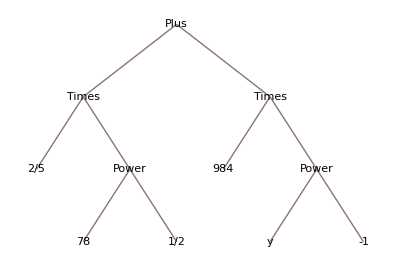

```mathematica
TreeForm[Sqrt[2+x]/5+x/y]
```

```mathematica
Clear[n]
Apply[Plus,Range[3,n+2]^n]
```

Range::range: Range specification in Range[3,2+n] does not have appropriate bounds.

n+Range[3,2+n]

```mathematica
f[n_]=Apply[Plus,Range[3,n+2]^n]
```

Range::range: Range specification in Range[3,2+n] does not have appropriate bounds.

n+Range[3,2+n]

```mathematica
f[n_]=Range[3,n+2]^n
```

Range::range: Range specification in Range[3,2+n] does not have appropriate bounds.

Range[3,2+n]^n

```mathematica
Select[Range[1000],Apply[Plus,Range[3,#+2]^#]==(#+3)^#&]
```

{2,3}

```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

```mathematica
Range[3,n]
```

Range::range: Range specification in Range[3,n] does not have appropriate bounds.

Range[3,n]

```mathematica
Range[n]
```

Range::range: Range specification in Range[n] does not have appropriate bounds.

Range[n]

```mathematica
f[n_]=List[3,n]
```

{3,n}

```mathematica
?List
```

{e_1,e_2,…} is a list of elements.

```mathematica
Table[]
```

```mathematica
cs[n_]:=Range[3,n+2]^n
```

```mathematica
cs[n_]:=Range[3,n+2]^n
Apply[Plus,cs[n_]]
```

Range::range: Range specification in Range[3,2+n_] does not have appropriate bounds.

n_+Range[3,2+n_]

```mathematica
Apply[Plus,cs[1000]]
```

11672217879321816498684472664929018945500327102817571054477525486785736634199274096773589371506159089911911040141993486060553231498741161579237330475731399188893440302152565061938089967483276489155676677485448225854517186673697633127728732435503899204795548700422038363565850308425845396024145287379407491182351172232937113654594340707955596024904163329863159670386670162414484836981823349496061782230123466374447176617038171724324954571259867710371203452722229104946136396031440047290607668597856890980263126947727750184491061372657130593911368754591098898682377663086867891328635462617321554766337371748144741338071655185226094497194957834276707970128849975739759737570223809814401551379878598717845430118493542991701053873065570232013704565306234701841874672244123245057018288952660821748717394481979681226213759166511329001621909672573471313177565871471969705509754954358503145945761797505368663889434887652313523923658651478750322041321706926039052412386162966979006291477751668275720328063412131840355683696270878700226396380893196340610513744735201762198480427423767570786066963577039859916395413160652391338840082020551099101343775681975060018013884574937613586633544368927679596104665668294574232337233028146565434736543471915301068269340803738459356161075482024242801467400011808709705364110107823405740209590783675905637617002005693398033302611490384429480471987558435840365044913058255873080825857013333101869749285756031260135044653644537899377551244990412338656932739717534875717586526531862467314259780977935475440090459687551288281247624746883209687844369156724916724093526052795980014571261935874442972238955891111338842429366910798841376687804524601428998506630241584062993895675998918805962959540819478677170162583525424117335826389803673167372242128401586721471848231971432835049508111353769277369695140846480246099718450607004645613617537316344332211467125188915498858904450517830086609090927302432476596424602935491160246666172899335584252930660257879412473903719649119733449400134768286635144409026468851058964718087744889089029109849505067425167347836454818262617402058482108578582184332936314820394813854902576992137343303283175891828923439549229024562086722153160619863125410171115512611077198984768895830373961951226806396811432688212722352491649823179791235020163815417502036787263102479408560437032640773715158765303890066275375755410609923389089189836305035761085506069717553090196316914792511754176467831941549188693777171862776380894076177993540547224714819284610290394075717279473453371895691557671623819443260950791825066113001397247573438156341663234530181664791483776002763947093102452706425051379121649237841889294006666231866839419092037075851550449534863253965712972637371069678723886206536084707329357719962402765837015034858544805530424909222023433978829484755187424880441317227664049105268283501461676739366701313684158210688492483949587521883952518756204229588166205416926060011854464475044280208168029597708496524408535068583869085699304486870349341066813300